0.633645 (-1+(1-ⅇ^(-2.3557 (-2.54697+x)))^2)

2.08004 (19825.7/x^12-140.804/x^6)

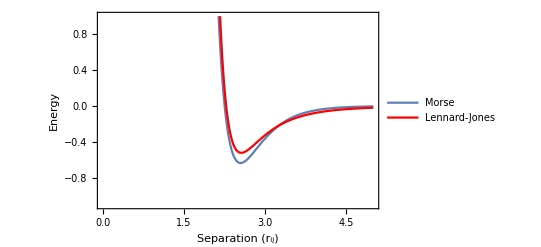

```mathematica
(* LJ and Morse potfit comparison - initial_morse_fit_230616 and initial_LJ_sanity_check230616*)

d=0.63364470;
a=2.35569970;
r=2.54697086;
e=0.52001096;
s=2.28087974;

morse = d*(((1-Exp[-a*(x-r)])^2)-1)
lj = 4*e(((s/x)^12)-((s/x)^6))

plotm = Plot[morse,{x,0,5},PlotRange->Automatic,PlotStyle->{Red}];
plotl = Plot[lj,{x,0,5}, PlotRange->{{0,5},{-1.1,1}}, PlotStyle->{Grey}];
both = Plot[{morse, lj},{x,0,5},PlotStyle->{Grey,Red}, PlotRange->{{0,5},{-1.1,1}},PlotLegends->Placed[{"Morse","Lennard-Jones"},{Scaled[{0.5,0.5}], {-0.2, -0.9}}],Frame-> True,FrameLabel->{"Separation (r_ij)","Energy"}]
GraphicsRow[{plotm, plotl, both},PlotRange->Automatic];
```